### Start choosing the example:

```mathematica
t=1;
beta=0;
A=0.2;
g[x]
```

Log[x]

```mathematica
Data=DataG[t]
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"];
Data=<|"Vertices List"->{1},"Adjacency Matrix"->{{0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{1,U1}},"Switching Costs"->{}|>;
```

```mathematica
(crit=CriticalCongestionSolver[d2e=Data2Equations[Data/.{I1->100,U1->0}]])//AbsoluteTiming
```

{True,True,True}

{0.047319,<|j2→100,j1→0,j3→0,j4→100,u4→0,jt1→100,jt2→0,u2→0,u3→0,u1→0|>}

D2E: Variables are all set

Second check:

-j1+jt2==0&&-j4+jt1==0

j1==jt2&&j4==jt1

The matrices B and K are: 
{(80
0
0),(1 | 0 | 0 | 0
1 | 0 | -1 | 1
0 | -1 | 1 | -1)}
The order of the variables is 
{j2,j4,jt1,jt2}

{u4→0}

D2E: CleanEqualities for the values at the auxiliary edges

D2E: Assembled most elements of the system

D2E: CleanEqualities for the switching conditions on each vertex: 
u3∈ℝ&&u2≤u3

D2E: CleanEqualities for the complementary conditions (given the rules)

D2E: CleanEqualities for the balance conditions in terms of (mostly) transition currents

Select::normal: Nonatomic expression expected at position 1 in Select[True,Head[#1]===Or&].

Select::normal: Nonatomic expression expected at position 1 in Select[True,Head[#1]=!=Or&].

D2E: CleanEqualities for the (non) critical case equations

D2E: D2E is finished!

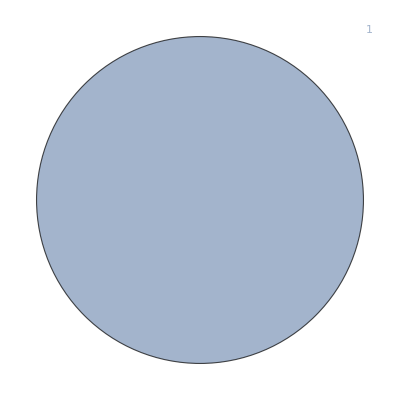
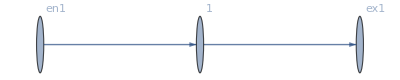
<|Vertices List→{1},Adjacency Matrix→{{0}},Entrance Vertices and Currents→{{1,80}},Exit Vertices and Terminal Costs→{{1,0}},Switching Costs→{},BG→-Graphics-,InEdges→{en1->1},OutEdges→{1->ex1},FG→-Graphics-,jvars→<|{en1,en1->1}→j1,{1,en1->1}→j2,{1,1->ex1}→j3,{ex1,1->ex1}→j4|>,jtvars→<|{1,en1->1,1->ex1}→jt1,{1,1->ex1,en1->1}→jt2|>,uvars→<|{en1,en1->1}→u1,{1,en1->1}→u2,{1,1->ex1}→u3,{ex1,1->ex1}→u4|>,costpluscurrents→<||>,jays→<||>,AllOr→Select[True,Head[#1]===Or&],AllIneq→Select[True,Head[#1]=!=Or&],EqPosJs→j1≥0&&j2≥0&&j3≥0&&j4≥0,EqPosJts→jt1≥0&&jt2≥0,EqPosCon→True,EqCurrentCompCon→(j1==0||j2==0)&&(j3==0||j4==0),EqTransitionCompCon→jt1==0||jt2==0,EqAllAll→MFGraphs`Private`EqAllAll$7913,BoundaryRules→<|j1→0,j4→80,j2→80,j3→0,u4→0,u2→0,u3→0,jt2→0,jt1→80,u1→0|>,InitRules→<|j1→0,j4→80,j2→80,j3→0,u4→0,u2→0,u3→0,jt2→0,jt1→80,u1→0|>,RulesCriticalCase→<|j1→0,j4→80,j2→80,j3→0,u4→0,u2→0,u3→0,jt2→0,jt1→80,u1→0|>,RulesCriticalCase1→{{}},RuleExitValues→{u4→0},RuleEntryIn→{j2→80,j1→0},Nlhs→{},MinimalTimeRhs→{},EqCriticalCase→True,EqNonCritical→True,RuleNonCritical→<|j1→0,j4→80,j2→80,j3→0,u4→0,u2→0,u3→0,jt2→0,jt1→80,u1→0|>,RuleNonCritical1→{{}},EqSwitchingConditions→u2≤u3,EqValueAuxiliaryEdges→u2==u1&&u4==u3,EqBalanceSplittingCurrents→j2==jt1&&j3==jt2,EqBalanceGatheringCurrents→j1==jt2&&j4==jt1,Nrhs→{},B→SparseArray[…],K→SparseArray[…],NoDeadEnds→{{1,en1->1},{1,1->ex1}},NoDeadStarts→{{en1,en1->1},{ex1,1->ex1}},EqEntryIn→{j2==80},vars→{j2,j4,jt1,jt2}|>

```mathematica
d2e=D2E[Data/.{I1-> 80, U1-> 0}]
```

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1-> 80, U1-> 15}]])//AbsoluteTiming
```

Variables are all set

CleanEqualities for the values at the auxiliary edges

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the (non) critical case equations

CCS2: EliminateVarsSimplify for the us

CCS2: Finished with the us!

CCS2: Done!

{0.048474,<|u1→15,u2→15,u3→15,u4→15,j1→0,j2→80,j3→0,j4→80|>}

```mathematica
(rule=CriticalCongestionSolver2[d2e])//AbsoluteTiming
```

CCS2: EliminateVarsSimplify for the us

CCS2: Finished with the us!

CCS2: Done!

{0.00163,<|u1→15,u2→15,u3→15,u4→15,j1→0,j2→80,j3→0,j4→80|>}

### Non-critical congestion

```mathematica
Cost[current_,edge_]
```

IntM[current_,edge_]

```mathematica
Cost[a_,b_]:= -a
```

```mathematica
Cost[a_,b_]:= 0
```

```mathematica
d2e=D2E[Data/.{I1-> 80, U1-> 15}];
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the (non) critical case equations

```mathematica
alpha =0;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

<|u1→15,u2→15,u3→15,u4→15,j1→0,j2→80,j3→0,j4→80|>

```mathematica
alpha =0.5;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

<|u1→15,u2→15,u3→15,u4→15,j1→0,j2→80,j3→0,j4→80|>

```mathematica
alpha =1;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

<|u1→15,u2→15,u3→15,u4→15,j1→0,j2→80,j3→0,j4→80|>

```mathematica
alpha =1.5;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

<|u1→15,u2→15,u3→15,u4→15,j1→0,j2→80,j3→0,j4→80|>

```mathematica
alpha =2;
FFR=FixedPoint[FixedReduce2[d2e],<||>,10]
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

EliminateVarsSimplify for the us

Finished with the us!

Done!

<|u1→15,u2→15,u3→15,u4→15,j1→0,j2→80,j3→0,j4→80|>

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1},Adjacency Matrix→{{0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{1,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15}];//Timing
```

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 1.×10^-6 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
True
and the rules are:
<|j247→80,u256→15,j248→80,j249→0,j250→0,jt251→80,jt252→0,u254→15,u255→15,u253→15|>

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.008188,Null}

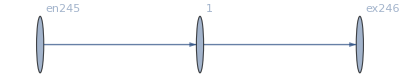

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j247→80,j248→80,j249→0,j250→0,jt251→80,jt252→0,u253→15,u254→15,u255→15,u256→15|>

#### Non-linear case

```mathematica
alpha=0;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: nonlinear: 
True

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1,Norm[{}]]

<|j247→80,j248→80,j249→0,j250→0,jt251→80,jt252→0,u253→15,u254→15,u255→15,u256→15|>

```mathematica
alpha=0.1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1,Norm[{}]]

<|j283→80,j284→80,j285→0.,j286→0.,jt287→80,jt288→0.,u289→15.,u290→15.,u291→15.,u292→15.|>

```mathematica
alpha=0.3;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1,Norm[{}]]

<|j13→80,j14→80,j15→0.,j16→0.,jt17→80,jt18→0.,u19→15.,u20→15.,u21→15.,u22→15.|>

```mathematica
alpha=1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1,Norm[{}]]

<|j13→80,j14→80,j15→0.,j16→0.,jt17→80,jt18→0.,u19→15.,u20→15.,u21→15.,u22→15.|>

```mathematica
alpha=1.2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1,Norm[{}]]

<|j13→80,j14→80,j15→0.,j16→0.,jt17→80,jt18→0.,u19→15.,u20→15.,u21→15.,u22→15.|>

```mathematica
alpha=1.6;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1,Norm[{}]]

<|j13→80,j14→80,j15→0.,j16→0.,jt17→80,jt18→0.,u19→15.,u20→15.,u21→15.,u22→15.|>

```mathematica
alpha=1.9;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1,Norm[{}]]

<|j13→80,j14→80,j15→0.,j16→0.,jt17→80,jt18→0.,u19→15.,u20→15.,u21→15.,u22→15.|>

```mathematica
alpha=2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1,Norm[{}]]

<|j13→80,j14→80,j15→0.,j16→0.,jt17→80,jt18→0.,u19→15.,u20→15.,u21→15.,u22→15.|>